Effect of Temperature on Partial Miscibility in a Binary-Liquid System

```mathematica
Manipulate[
Module[{a,b,r,GibbsEnergy,molarComposition1,molarComposition2,beaker,plot},
a=7500;b=1000;r=8.314 ;(*J/mol*) 

GibbsEnergy [x_]:=x*(1-x)*(a+b*(1-2*x))+r*t*(x*Log[x]+(1-x)Log[1-x]);
molarComposition1=x/.Last[FindMinimum[{GibbsEnergy[x],{x>0, x<1}},{x,0.0001}]];
molarComposition2= x/.Last[FindMinimum[{GibbsEnergy[x],{x>0, x<1}},{x,0.9999}]];


beaker=Graphics3D[{
{Opacity@0.3,Cylinder[{{0,0,0},{0,0,1.75}},1]},
{EdgeForm@None,
If[molarComposition1==molarComposition2,
{Opacity[0.8,Blend[{Blue,RGBColor[0,0.6,0]},0.5]],Cylinder [{{0,0,0}, {0,0,1.5}}, 1],
Text[Framed[Style[Column[{"mole fraction",NumberForm[molarComposition1,{2,2}]},Center],18,Black],Background->White,FrameStyle->None,FrameMargins->Small],{0,0,0.75}]},
{Opacity[0.8,Blue],Cylinder [{{0,0,0}, {0,0, 0.75}}, 1],Opacity [0.8,RGBColor[0,0.6,0]],Cylinder [{{0,0,0.75}, {0,0, 1.5}}, 1],
Text[Framed[Style[NumberForm[#1,{2,2}],18,Black],Background->White,FrameStyle->None,FrameMargins->Small],{0,0,#2}]&@@@{{molarComposition1,0.375},{molarComposition2,1.125}}}]}
 },Boxed->False,ViewPoint->{0,3.5,0},ImageSize->{200,425},AspectRatio->2];

plot=Plot[GibbsEnergy[x], {x, 0.0001, 0.9999},PlotStyle->{Thick,Black},PlotRangePadding->{None,Scaled@0.02},
Axes->False,Frame->True,FrameLabel->{"mole fraction", "change in Gibbs free energy (J/mol)"},LabelStyle->{17,Black},ImageSize->{400,425},AspectRatio->Full,
Epilog->{
Line[{{0,0},{1,0}}],
If[molarComposition1≠molarComposition2,{
{Dashed,
Blue,Line[{{molarComposition1,GibbsEnergy[molarComposition1]}, {molarComposition1, 0}}],
RGBColor[0,0.6,0],Line[{{molarComposition2,GibbsEnergy[molarComposition2]}, {molarComposition2, 0}}]},
{PointSize@0.03,Blue,Point[{molarComposition1,GibbsEnergy[molarComposition1]}],RGBColor[0,0.6,0], Point[{molarComposition2,GibbsEnergy[molarComposition2]}]}
}]
}];

Grid@{{plot,beaker}}
],
Control[{{t,273,"temperature (K)"},273,523,10,Appearance->"Labeled" }]
]
```

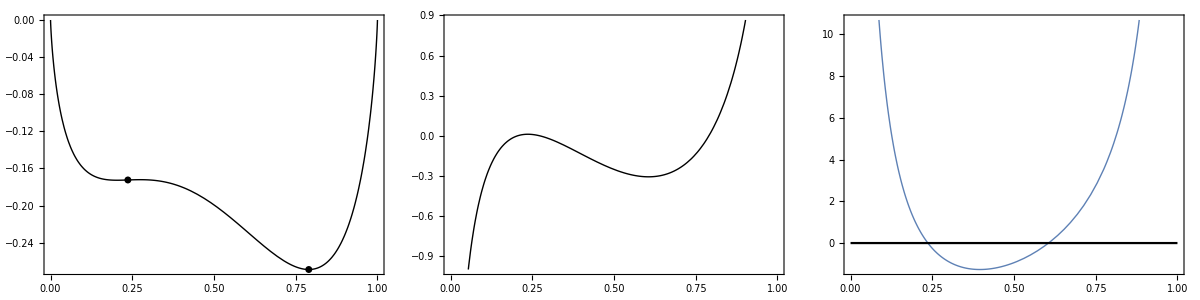

```mathematica
Module[{y,dy,ddy,pt1,pt2,opt},
y[x_]:=(1.64-1.64*x) Log[1-x]+x (4.25-5.25* x+x^2+1.64*Log[x]);
dy[x_]:=y'[x];
ddy[x_]:=dy'[x];

pt1=x/.FindRoot[ddy[x]==0,{x,0.01}];
pt2=x/.FindRoot[dy[x]==0,{x,0.99}];

opt=Sequence[PlotStyle->{Thick,Black},Frame->True,ImageSize->{250,250},AspectRatio->1];

Grid@{{Plot[y[x],{x,0,1},Evaluate@opt,Epilog->{PointSize@0.02,Point@{pt1,y[pt1]},Point@{pt2,y[pt2]}}],Plot[dy[x],{x,0,1},Evaluate@opt],Plot[{ddy[x],0},{x,0,1},Evaluate@opt]}}
]
```

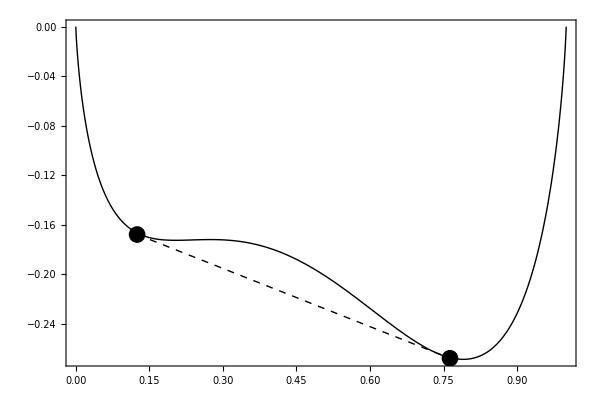

```mathematica
Module[{y},
y[x_]:=(1.64-1.64*x) Log[1-x]+x (4.25-5.25* x+x^2+1.64*Log[x]);

Plot[y[x],{x,0,1},PlotStyle->{Thick,Black},Frame->True,FrameTicks->True,LabelStyle->{17,Black},ImageSize->{600,400},AspectRatio->Full,
Epilog->{
PointSize@0.02,Point@{0.125,-0.168},Point@{0.763,-0.268},
Thick,Dashed,Line[{{0.125,-0.168},{0.763,-0.268}}]
}]
]
```

This Demonstration shows how the mole fractions of a binary liquid system, composed of two partially miscible liquids, change with temperature. Varying the temperature changes the Gibbs free energy, as shown in the graph. Two phases co-exist when a tangent line (orange dashed line) connecting the two parts of the curves yield a lower Gibbs free energy than one phase for the range of compositions between the two points on the graph. The representation of two liquid phases on the right indicates when two liquid phases exist but it does not represent the amounts of each phase, since that depends on the overall composition of the system.

References

[1] S. R. Logan, “The Behavior of a Pair of Partially Miscible Liquids,” Journal of Chemical Education, 75(3), 1998 p. 339. doi:10.1021/ed075p339.

[2] J. P. Erikson, “Partially Miscible Water-Triethylamine Solutions and Their Temperature Dependence,” Journal of Chemical Education, 94(1), 2017 pp. 75–78. doi:10.1021/acs.jchemed.6b00489.

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

partial miscibility

Contributed by: Kaiyuan Tang

Additional contributions by: Rachael L. Baumann and John L. Falconer